(108 x (-π/2+x) (-π/3+x))/π^3

-(108 x (-π/2+x) (-π/6+x))/π^3

(36 x (-π/3+x) (-π/6+x))/π^3

(54 x (-π/2+x) (-π/3+x))/π^3-(54 √3 x (-π/2+x) (-π/6+x))/π^3+(36 x (-π/3+x) (-π/6+x))/π^3

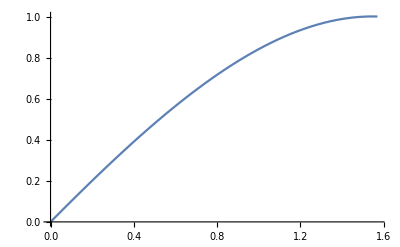

```mathematica
L1[x_]=(x*(x-Pi/3)*(x-Pi/2))/((Pi/6)*(Pi/6-Pi/3)*(Pi/6-Pi/2))
L2[x_]=(x*(x-Pi/6)*(x-Pi/2))/((Pi/3)*(Pi/3-Pi/6)*(Pi/3-Pi/2))
L3[x_]=(x*(x-Pi/6)*(x-Pi/3))/((Pi/2)*(Pi/2-Pi/6)*(Pi/2-Pi/3))
P[x_]=1/2*L1[x]+(Sqrt[3]/2)*L2[x]+L3[x]
Plot[P[x],{x,0,Pi/2}]
```

```mathematica
P[Pi/5] //N
```

0.587061

```mathematica
absErr = Sin[Pi/5] - P[Pi/5]
```

-2/5-(27 √3)/250+√(5/8-(√5)/8)

```mathematica
absErr = Sin[Pi/5] - P[Pi/5] //N
```

0.000723765

```mathematica
R[x_] = Expand[Sin[x] - P[x]] //N
```

-1.02043 x+0.0654708 x^2+0.113872 x^3+Sin[x]

-(11 x)/π+(9 √3 x)/(2 π)+(63 x^2)/π^2-(36 √3 x^2)/π^2-(90 x^3)/π^3+(54 √3 x^3)/π^3+Sin[x]

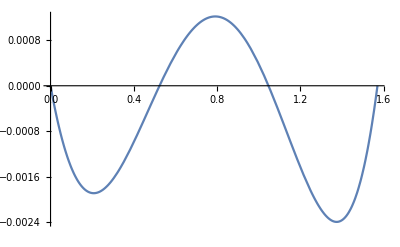

```mathematica
Plot[R[x], {x, 0, Pi/2}]
```

```mathematica
AbsErr[x_] = Sin[x] - P[x]
```

-(54 x (-π/2+x) (-π/3+x))/π^3+(54 √3 x (-π/2+x) (-π/6+x))/π^3-(36 x (-π/3+x) (-π/6+x))/π^3+Sin[x]

```mathematica
Plot[AbsErr[x], {x, 0, Pi/2}]
```

-Graphics-

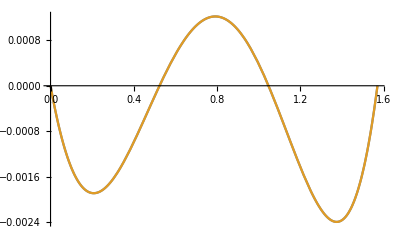

```mathematica
Plot[{R[x], AbsErr[x]}, {x, 0, Pi/2}]
```

```mathematica
MaxR[x_] = Abs[x*(x-Pi/6)*(x-Pi/3)*(x-Pi/2)/24]
```

1/24 Abs[x (-π/2+x) (-π/3+x) (-π/6+x)]

```mathematica
Abs[-3]
```

3

```mathematica
MaxR[x] //N
```

0.0416667 Abs[(-1.5708+x) (-1.0472+x) (-0.523599+x) x]

```mathematica
MaxR[x_] = |x*(x-Pi/6)*(x-Pi/3)*(x-Pi/2)|/24
```

Syntax::sntxf: "MaxR[x_] =" cannot be followed by "| x * (x - Pi/6) * (x - Pi/3) * (x - Pi/2) |/24""".

```mathematica
MaxR[x_] = Abs[x*(x-Pi/6)*(x-Pi/3)*(x-Pi/2)/24]
```

1/24 Abs[x (-π/2+x) (-π/3+x) (-π/6+x)]

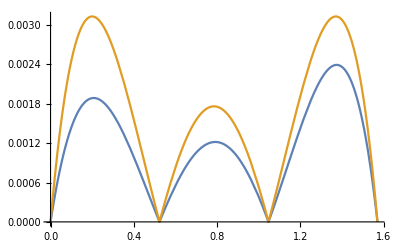

```mathematica
Plot[{Abs[R[x]], MaxR[x]}, {x, 0, Pi/2}]
```

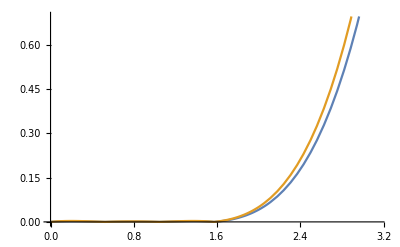

```mathematica
Plot[{Abs[R[x]], MaxR[x]}, {x, 0, Pi}]
```

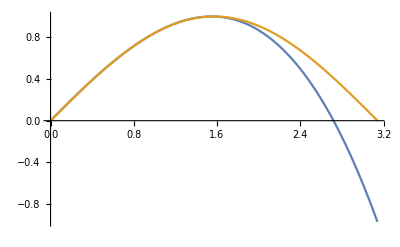

```mathematica
Plot[{P[x], Sin[x]}, {x, 0, Pi}]
```

```mathematica
Sum[x, y]
```

x y

```mathematica
Sum[{a, b}]
```

Sum::argmu: Sum called with 1 argument; 2 or more arguments are expected.

Sum[{a,b}]

```mathematica
L_0[_x] = ((x - Pi/6)*(x-Pi/3)*(x-Pi/2)) / ((-Pi/2)*(-Pi/3)*(-Pi/2))
```

Set::write: Tag Times in 0[_x]\ L_ is Protected.

-(12 (-π/2+x) (-π/3+x) (-π/6+x))/π^3

```mathematica
L0[x_] = ((x - Pi/6)*(x-Pi/3)*(x-Pi/2)) / ((-Pi/2)*(-Pi/3)*(-Pi/2))
```

-(12 (-π/2+x) (-π/3+x) (-π/6+x))/π^3

```mathematica
S[x_] = L0[x] + L1[x] + L2[x] + L3[x] // Simplify
```

(π^3+22 π^2 x-72 π x^2+72 x^3)/(3 π^3)

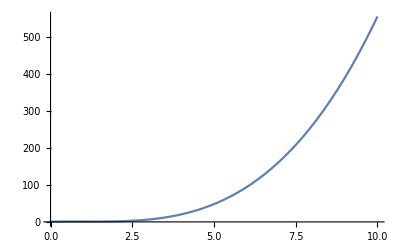

```mathematica
Plot[S[x], {x, 0, Pi/2}]
```

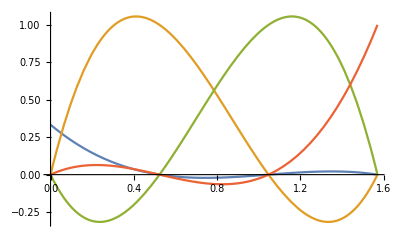

```mathematica
Plot[{L0[x], L1[x], L2[x], L3[x]}, {x, 0, Pi/2}]
```